# Analyze Märklin track signal

## Get complementary signals from digitizing car

### Load file

```mathematica
Directory[]
```

/home/cmaier/scad/Maerklin/analysis

```mathematica
Dimensions[raw=Import["MM2.78.fwd.csv"]]
```

{1048578,3}

```mathematica
Take[raw,12]
```

{{X,CH1,},{Second,Volt,},{-0.0589688,-17.2,},{-0.0589687,-17.2,},{-0.0589686,-17.2,},{-0.0589685,-17.2,},{-0.0589684,-17.2,},{-0.0589683,-17.2,},{-0.0589682,-17.2,},{-0.0589681,-17.2,},{-0.058968,-17.2,},{-0.0589679,-17.2,}}

### Convert into two time series

```mathematica
Dimensions[timeseries=Most/@Drop[raw,2]]
```

{1048576,2}

#### Calculate time step

```mathematica
Dimensions[ListConvolve[{1,-1},First/@#]&[timeseries]]
```

{1048575}

```mathematica
ListPlot[ListConvolve[{1,-1},First/@#],Frame->True,PlotRange->All]&[timeseries]
```

-Graphics-

```mathematica
{Min[#],Max[#]}&[ListConvolve[{1,-1},First/@#]]&[timeseries]
```

{1.×10^-7,1.×10^-7}

```mathematica
timestep=Median[ListConvolve[{1,-1},First/@#]]&[timeseries]
```

1.×10^-7

### Display

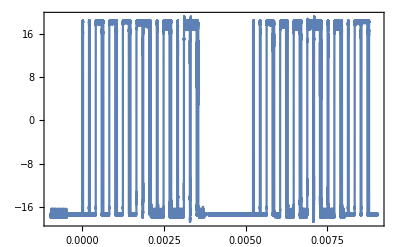

```mathematica
ListPlot[Take[#,{580000,680000}]&[timeseries],Frame->True,Joined->True]
```

## Digitize time series

```mathematica
Dimensions[digitized=Map[{#⟦1⟧,HeavisideTheta[#⟦2⟧-0.0001]}&,timeseries,{1}]]
```

{1048576,2}

### Display

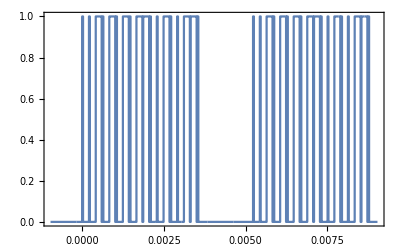

```mathematica
ListPlot[Take[#,{580000,680000}]&[digitized],Frame->True,Joined->True]
```

#### Display 500ms data transmission

```mathematica
ListPlot[Take[#,{380000,880000}]&/@MapThread[Function[{series, offset},#+{0,offset}&/@series],{{digitized},{0}}],Frame->True,Joined->True,PlotRange->All,FrameLabel->{"t [s]",""}]
```

-Graphics-

#### Runs of identical values for series

```mathematica
Map[Dimensions,runs=SplitBy[#,Last]&[digitized],{1}]
```

{{679,2},{1813,2},{263,2},{1812,2},{264,2},{263,2},{16743,2},{257,2},{1812,2},{260,2},{1811,2},{1812,2},{259,2},{260,2},{1815,2},{1814,2},{262,2},{258,2},{1813,2},{1815,2},{260,2},{260,2},{1816,2},{1813,2},{263,2},{1811,2},{260,2},{258,2},{1813,2},{1812,2},{264,2},{1811,2},{260,2},{1811,2},{259,2},{259,2},{1812,2},{1812,2},{264,2},{1812,2},{264,2},{262,2},{41633,2},{130,2},{906,2},{128,2},{907,2},{907,2},{130,2},{133,2},{905,2},{908,2},{133,2},{130,2},{907,2},{910,2},{129,2},{130,2},{905,2},{907,2},{130,2},{910,2},{129,2},{130,2},{906,2},{130,2},{905,2},{129,2},{907,2},{129,2},{907,2},{128,2},{907,2},{128,2},{908,2},{129,2},{911,2},{129,2},{8365,2},{128,2},{907,2},{128,2},{908,2},{906,2},{133,2},{130,2},{906,2},{906,2},{129,2},{130,2},{906,2},{906,2},{130,2},{128,2},{908,2},{909,2},{131,2},{905,2},{131,2},{128,2},{907,2},{129,2},{906,2},{129,2},{907,2},{128,2},{907,2},{129,2},{906,2},{129,2},{908,2},{133,2},{906,2},{130,2},{55661,2},{259,2},{1812,2},{259,2},{1812,2},{1812,2},{259,2},{260,2},{1816,2},{1812,2},{259,2},{258,2},{1814,2},{1817,2},{263,2},{258,2},{1812,2},{1812,2},{259,2},{1813,2},{263,2},{260,2},{1817,2},{262,2},{1813,2},{1817,2},{263,2},{1811,2},{260,2},{258,2},{1812,2},{258,2},{1813,2},{1812,2},{263,2},{260,2},{16744,2},{259,2},{1818,2},{263,2},{1811,2},{1814,2},{263,2},{258,2},{1814,2},{1815,2},{260,2},{259,2},{1817,2},{1811,2},{260,2},{260,2},{1816,2},{1812,2},{259,2},{1812,2},{260,2},{262,2},{1812,2},{260,2},{1812,2},{1811,2},{260,2},{1812,2},{258,2},{259,2},{1812,2},{260,2},{1816,2},{1812,2},{260,2},{257,2},{42637,2},{259,2},{1816,2},{260,2},{1817,2},{1812,2},{259,2},{258,2},{1812,2},{1813,2},{264,2},{257,2},{1814,2},{1816,2},{259,2},{259,2},{1817,2},{1811,2},{260,2},{1811,2},{259,2},{259,2},{1812,2},{1812,2},{259,2},{1812,2},{260,2},{1815,2},{259,2},{260,2},{1816,2},{259,2},{1812,2},{1814,2},{263,2},{258,2},{16740,2},{263,2},{1812,2},{259,2},{1813,2},{1812,2},{259,2},{260,2},{1816,2},{1814,2},{263,2},{258,2},{1814,2},{1815,2},{260,2},{260,2},{1816,2},{1813,2},{263,2},{1813,2},{258,2},{260,2},{1816,2},{1812,2},{259,2},{1812,2},{259,2},{1813,2},{264,2},{262,2},{1815,2},{262,2},{1814,2},{1816,2},{259,2},{260,2},{42639,2},{259,2},{1813,2},{257,2},{1813,2},{1813,2},{258,2},{259,2},{1814,2},{1816,2},{258,2},{260,2},{1816,2},{1812,2},{259,2},{259,2},{1813,2},{1812,2},{265,2},{1815,2},{260,2},{258,2},{1812,2},{259,2},{1812,2},{1813,2},{263,2},{1812,2},{259,2},{258,2},{1813,2},{258,2},{1813,2},{1812,2},{260,2},{259,2},{16742,2},{259,2},{1813,2},{258,2},{1813,2},{1812,2},{260,2},{263,2},{1812,2},{1812,2},{259,2},{260,2},{1816,2},{1812,2},{259,2},{259,2},{1813,2},{1812,2},{265,2},{1815,2},{261,2},{262,2},{1814,2},{263,2},{1818,2},{1810,2},{260,2},{1812,2},{260,2},{259,2},{1812,2},{258,2},{1814,2},{1816,2},{259,2},{259,2},{42638,2},{258,2},{1812,2},{259,2},{1813,2},{1812,2},{259,2},{259,2},{1818,2},{1816,2},{263,2},{260,2},{1816,2},{1812,2},{260,2},{260,2},{1816,2},{1812,2},{264,2},{1812,2},{264,2},{258,2},{1814,2},{263,2},{1812,2},{1812,2},{259,2},{260,2},{1816,2},{260,2},{1817,2},{1812,2},{264,2},{1811,2},{260,2},{258,2},{16739,2},{260,2},{1816,2},{259,2},{1812,2},{1812,2},{260,2},{257,2},{1814,2},{1811,2},{260,2},{263,2},{1812,2},{1813,2},{258,2},{260,2},{1816,2},{1812,2},{259,2},{1813,2},{259,2},{258,2},{1814,2},{262,2},{1813,2},{1812,2},{259,2},{259,2},{1812,2},{260,2},{1816,2},{1812,2},{259,2},{1812,2},{259,2},{259,2},{42636,2},{262,2},{1813,2},{259,2},{1812,2},{1811,2},{260,2},{258,2},{1812,2},{1812,2},{259,2},{259,2},{1817,2},{1812,2},{259,2},{258,2},{1812,2},{1814,2},{263,2},{1811,2},{260,2},{263,2},{1812,2},{260,2},{1817,2},{1812,2},{264,2},{1810,2},{261,2},{263,2},{1813,2},{257,2},{1813,2},{1812,2},{260,2},{259,2},{16741,2},{260,2},{1816,2},{258,2},{1812,2},{1814,2},{263,2},{258,2},{1813,2},{1816,2},{259,2},{259,2},{1817,2},{1812,2},{264,2},{258,2},{1813,2},{1817,2},{264,2},{1811,2},{260,2},{258,2},{1813,2},{263,2},{1812,2},{1816,2},{262,2},{1815,2},{259,2},{260,2},{1817,2},{258,2},{1812,2},{1814,2},{263,2},{258,2},{42643,2},{259,2},{1812,2},{259,2},{1813,2},{1811,2},{260,2},{263,2},{1812,2},{1812,2},{259,2},{260,2},{1816,2},{1812,2},{259,2},{259,2},{1813,2},{1812,2},{265,2},{1815,2},{259,2},{259,2},{1814,2},{262,2},{1812,2},{1813,2},{259,2},{1813,2},{259,2},{258,2},{1812,2},{1814,2},{263,2},{1812,2},{260,2},{263,2},{16737,2},{263,2},{1812,2},{259,2},{1813,2},{1812,2},{264,2},{257,2},{1814,2},{1815,2},{261,2},{262,2},{1813,2},{1812,2},{259,2},{260,2},{1817,2},{1812,2},{263,2},{1812,2},{260,2},{257,2},{1814,2},{263,2},{1818,2},{1816,2},{263,2},{1813,2},{264,2},{264,2},{1817,2},{1812,2},{263,2},{1811,2},{260,2},{258,2},{42645,2},{264,2},{1816,2},{259,2},{1812,2},{1813,2},{264,2},{257,2},{1814,2},{1816,2},{259,2},{260,2},{1817,2},{1815,2},{261,2},{262,2},{1814,2},{1817,2},{259,2},{1812,2},{265,2},{262,2},{1813,2},{258,2},{1812,2},{1813,2},{263,2},{1812,2},{259,2},{259,2},{1813,2},{258,2},{1812,2},{1814,2},{264,2},{257,2},{16745,2},{257,2},{1813,2},{259,2},{1812,2},{1812,2},{260,2},{258,2},{1813,2},{1816,2},{259,2},{260,2},{1817,2},{1812,2},{264,2},{258,2},{639,2}}

```mathematica
Length[runs]
```

599

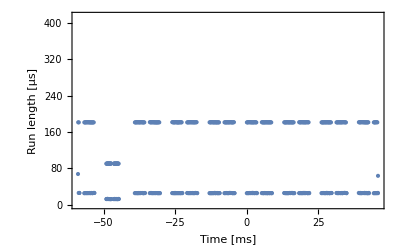

```mathematica
ListPlot[{10^3 First[First[#]],10^6 timestep Length[#]}&/@#,Frame->True,FrameLabel->{"Time [ms]","Run length [μs]"}]&[runs]
```

There is one outlier in the MM2 packet sequence ... maybe a switch packet?

## Packets within the time series

### Short data packets

MM format, see 2.2.9 Einbettung von Steuerbefehlen im MM-Format

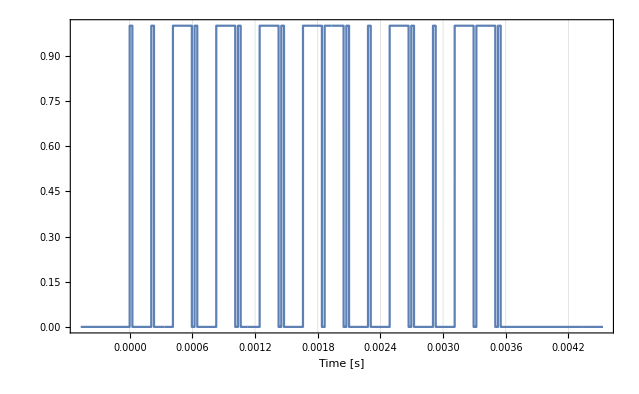

```mathematica
ListPlot[Take[#,{585000,635000}],Frame->True,Joined->True,FrameLabel->{"Time [s]",""},GridLines->{Range[-.15,.15,1.*^-4],None}]&[digitized]
```

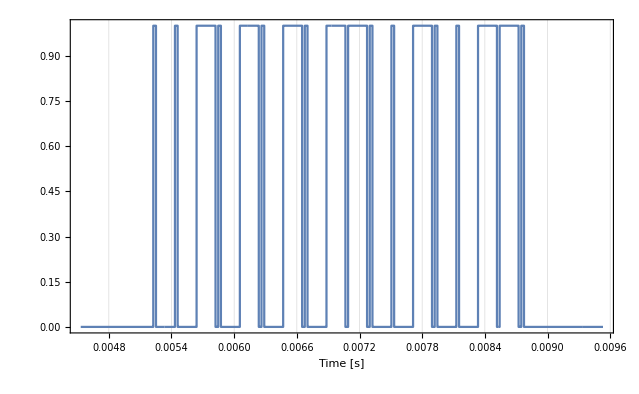

```mathematica
ListPlot[Take[#,{635000,685000}],Frame->True,Joined->True,FrameLabel->{"Time [s]",""},GridLines->{Range[-.15,.15,1.*^-4],None}]&[digitized]
```

## Run length decoding

#### bit frame (100μs) per sampling step

```mathematica
timestep/10^-4
```

0.001

#### Get run lengths of full traces

```mathematica
Length[fullruns=SplitBy[#,Last]&[digitized]]
```

599

### Run lengths in bit frames

```mathematica
rlbits=Map[timestep/10^-4 Length[#]&,fullruns,{1}]
```

{0.679,1.813,0.263,1.812,0.264,0.263,16.743,0.257,1.812,0.26,1.811,1.812,0.259,0.26,1.815,1.814,0.262,0.258,1.813,1.815,0.26,0.26,1.816,1.813,0.263,1.811,0.26,0.258,1.813,1.812,0.264,1.811,0.26,1.811,0.259,0.259,1.812,1.812,0.264,1.812,0.264,0.262,41.633,0.13,0.906,0.128,0.907,0.907,0.13,0.133,0.905,0.908,0.133,0.13,0.907,0.91,0.129,0.13,0.905,0.907,0.13,0.91,0.129,0.13,0.906,0.13,0.905,0.129,0.907,0.129,0.907,0.128,0.907,0.128,0.908,0.129,0.911,0.129,8.365,0.128,0.907,0.128,0.908,0.906,0.133,0.13,0.906,0.906,0.129,0.13,0.906,0.906,0.13,0.128,0.908,0.909,0.131,0.905,0.131,0.128,0.907,0.129,0.906,0.129,0.907,0.128,0.907,0.129,0.906,0.129,0.908,0.133,0.906,0.13,55.661,0.259,1.812,0.259,1.812,1.812,0.259,0.26,1.816,1.812,0.259,0.258,1.814,1.817,0.263,0.258,1.812,1.812,0.259,1.813,0.263,0.26,1.817,0.262,1.813,1.817,0.263,1.811,0.26,0.258,1.812,0.258,1.813,1.812,0.263,0.26,16.744,0.259,1.818,0.263,1.811,1.814,0.263,0.258,1.814,1.815,0.26,0.259,1.817,1.811,0.26,0.26,1.816,1.812,0.259,1.812,0.26,0.262,1.812,0.26,1.812,1.811,0.26,1.812,0.258,0.259,1.812,0.26,1.816,1.812,0.26,0.257,42.637,0.259,1.816,0.26,1.817,1.812,0.259,0.258,1.812,1.813,0.264,0.257,1.814,1.816,0.259,0.259,1.817,1.811,0.26,1.811,0.259,0.259,1.812,1.812,0.259,1.812,0.26,1.815,0.259,0.26,1.816,0.259,1.812,1.814,0.263,0.258,16.74,0.263,1.812,0.259,1.813,1.812,0.259,0.26,1.816,1.814,0.263,0.258,1.814,1.815,0.26,0.26,1.816,1.813,0.263,1.813,0.258,0.26,1.816,1.812,0.259,1.812,0.259,1.813,0.264,0.262,1.815,0.262,1.814,1.816,0.259,0.26,42.639,0.259,1.813,0.257,1.813,1.813,0.258,0.259,1.814,1.816,0.258,0.26,1.816,1.812,0.259,0.259,1.813,1.812,0.265,1.815,0.26,0.258,1.812,0.259,1.812,1.813,0.263,1.812,0.259,0.258,1.813,0.258,1.813,1.812,0.26,0.259,16.742,0.259,1.813,0.258,1.813,1.812,0.26,0.263,1.812,1.812,0.259,0.26,1.816,1.812,0.259,0.259,1.813,1.812,0.265,1.815,0.261,0.262,1.814,0.263,1.818,1.81,0.26,1.812,0.26,0.259,1.812,0.258,1.814,1.816,0.259,0.259,42.638,0.258,1.812,0.259,1.813,1.812,0.259,0.259,1.818,1.816,0.263,0.26,1.816,1.812,0.26,0.26,1.816,1.812,0.264,1.812,0.264,0.258,1.814,0.263,1.812,1.812,0.259,0.26,1.816,0.26,1.817,1.812,0.264,1.811,0.26,0.258,16.739,0.26,1.816,0.259,1.812,1.812,0.26,0.257,1.814,1.811,0.26,0.263,1.812,1.813,0.258,0.26,1.816,1.812,0.259,1.813,0.259,0.258,1.814,0.262,1.813,1.812,0.259,0.259,1.812,0.26,1.816,1.812,0.259,1.812,0.259,0.259,42.636,0.262,1.813,0.259,1.812,1.811,0.26,0.258,1.812,1.812,0.259,0.259,1.817,1.812,0.259,0.258,1.812,1.814,0.263,1.811,0.26,0.263,1.812,0.26,1.817,1.812,0.264,1.81,0.261,0.263,1.813,0.257,1.813,1.812,0.26,0.259,16.741,0.26,1.816,0.258,1.812,1.814,0.263,0.258,1.813,1.816,0.259,0.259,1.817,1.812,0.264,0.258,1.813,1.817,0.264,1.811,0.26,0.258,1.813,0.263,1.812,1.816,0.262,1.815,0.259,0.26,1.817,0.258,1.812,1.814,0.263,0.258,42.643,0.259,1.812,0.259,1.813,1.811,0.26,0.263,1.812,1.812,0.259,0.26,1.816,1.812,0.259,0.259,1.813,1.812,0.265,1.815,0.259,0.259,1.814,0.262,1.812,1.813,0.259,1.813,0.259,0.258,1.812,1.814,0.263,1.812,0.26,0.263,16.737,0.263,1.812,0.259,1.813,1.812,0.264,0.257,1.814,1.815,0.261,0.262,1.813,1.812,0.259,0.26,1.817,1.812,0.263,1.812,0.26,0.257,1.814,0.263,1.818,1.816,0.263,1.813,0.264,0.264,1.817,1.812,0.263,1.811,0.26,0.258,42.645,0.264,1.816,0.259,1.812,1.813,0.264,0.257,1.814,1.816,0.259,0.26,1.817,1.815,0.261,0.262,1.814,1.817,0.259,1.812,0.265,0.262,1.813,0.258,1.812,1.813,0.263,1.812,0.259,0.259,1.813,0.258,1.812,1.814,0.264,0.257,16.745,0.257,1.813,0.259,1.812,1.812,0.26,0.258,1.813,1.816,0.259,0.26,1.817,1.812,0.264,0.258,0.639}

#### Run length encoded data packets separated by run length >2 bits

```mathematica
rlruns=SplitBy[#,#>2&]&[rlbits]
```

{{0.679,1.813,0.263,1.812,0.264,0.263},{16.743},{0.257,1.812,0.26,1.811,1.812,0.259,0.26,1.815,1.814,0.262,0.258,1.813,1.815,0.26,0.26,1.816,1.813,0.263,1.811,0.26,0.258,1.813,1.812,0.264,1.811,0.26,1.811,0.259,0.259,1.812,1.812,0.264,1.812,0.264,0.262},{41.633},{0.13,0.906,0.128,0.907,0.907,0.13,0.133,0.905,0.908,0.133,0.13,0.907,0.91,0.129,0.13,0.905,0.907,0.13,0.91,0.129,0.13,0.906,0.13,0.905,0.129,0.907,0.129,0.907,0.128,0.907,0.128,0.908,0.129,0.911,0.129},{8.365},{0.128,0.907,0.128,0.908,0.906,0.133,0.13,0.906,0.906,0.129,0.13,0.906,0.906,0.13,0.128,0.908,0.909,0.131,0.905,0.131,0.128,0.907,0.129,0.906,0.129,0.907,0.128,0.907,0.129,0.906,0.129,0.908,0.133,0.906,0.13},{55.661},{0.259,1.812,0.259,1.812,1.812,0.259,0.26,1.816,1.812,0.259,0.258,1.814,1.817,0.263,0.258,1.812,1.812,0.259,1.813,0.263,0.26,1.817,0.262,1.813,1.817,0.263,1.811,0.26,0.258,1.812,0.258,1.813,1.812,0.263,0.26},{16.744},{0.259,1.818,0.263,1.811,1.814,0.263,0.258,1.814,1.815,0.26,0.259,1.817,1.811,0.26,0.26,1.816,1.812,0.259,1.812,0.26,0.262,1.812,0.26,1.812,1.811,0.26,1.812,0.258,0.259,1.812,0.26,1.816,1.812,0.26,0.257},{42.637},{0.259,1.816,0.26,1.817,1.812,0.259,0.258,1.812,1.813,0.264,0.257,1.814,1.816,0.259,0.259,1.817,1.811,0.26,1.811,0.259,0.259,1.812,1.812,0.259,1.812,0.26,1.815,0.259,0.26,1.816,0.259,1.812,1.814,0.263,0.258},{16.74},{0.263,1.812,0.259,1.813,1.812,0.259,0.26,1.816,1.814,0.263,0.258,1.814,1.815,0.26,0.26,1.816,1.813,0.263,1.813,0.258,0.26,1.816,1.812,0.259,1.812,0.259,1.813,0.264,0.262,1.815,0.262,1.814,1.816,0.259,0.26},{42.639},{0.259,1.813,0.257,1.813,1.813,0.258,0.259,1.814,1.816,0.258,0.26,1.816,1.812,0.259,0.259,1.813,1.812,0.265,1.815,0.26,0.258,1.812,0.259,1.812,1.813,0.263,1.812,0.259,0.258,1.813,0.258,1.813,1.812,0.26,0.259},{16.742},{0.259,1.813,0.258,1.813,1.812,0.26,0.263,1.812,1.812,0.259,0.26,1.816,1.812,0.259,0.259,1.813,1.812,0.265,1.815,0.261,0.262,1.814,0.263,1.818,1.81,0.26,1.812,0.26,0.259,1.812,0.258,1.814,1.816,0.259,0.259},{42.638},{0.258,1.812,0.259,1.813,1.812,0.259,0.259,1.818,1.816,0.263,0.26,1.816,1.812,0.26,0.26,1.816,1.812,0.264,1.812,0.264,0.258,1.814,0.263,1.812,1.812,0.259,0.26,1.816,0.26,1.817,1.812,0.264,1.811,0.26,0.258},{16.739},{0.26,1.816,0.259,1.812,1.812,0.26,0.257,1.814,1.811,0.26,0.263,1.812,1.813,0.258,0.26,1.816,1.812,0.259,1.813,0.259,0.258,1.814,0.262,1.813,1.812,0.259,0.259,1.812,0.26,1.816,1.812,0.259,1.812,0.259,0.259},{42.636},{0.262,1.813,0.259,1.812,1.811,0.26,0.258,1.812,1.812,0.259,0.259,1.817,1.812,0.259,0.258,1.812,1.814,0.263,1.811,0.26,0.263,1.812,0.26,1.817,1.812,0.264,1.81,0.261,0.263,1.813,0.257,1.813,1.812,0.26,0.259},{16.741},{0.26,1.816,0.258,1.812,1.814,0.263,0.258,1.813,1.816,0.259,0.259,1.817,1.812,0.264,0.258,1.813,1.817,0.264,1.811,0.26,0.258,1.813,0.263,1.812,1.816,0.262,1.815,0.259,0.26,1.817,0.258,1.812,1.814,0.263,0.258},{42.643},{0.259,1.812,0.259,1.813,1.811,0.26,0.263,1.812,1.812,0.259,0.26,1.816,1.812,0.259,0.259,1.813,1.812,0.265,1.815,0.259,0.259,1.814,0.262,1.812,1.813,0.259,1.813,0.259,0.258,1.812,1.814,0.263,1.812,0.26,0.263},{16.737},{0.263,1.812,0.259,1.813,1.812,0.264,0.257,1.814,1.815,0.261,0.262,1.813,1.812,0.259,0.26,1.817,1.812,0.263,1.812,0.26,0.257,1.814,0.263,1.818,1.816,0.263,1.813,0.264,0.264,1.817,1.812,0.263,1.811,0.26,0.258},{42.645},{0.264,1.816,0.259,1.812,1.813,0.264,0.257,1.814,1.816,0.259,0.26,1.817,1.815,0.261,0.262,1.814,1.817,0.259,1.812,0.265,0.262,1.813,0.258,1.812,1.813,0.263,1.812,0.259,0.259,1.813,0.258,1.812,1.814,0.264,0.257},{16.745},{0.257,1.813,0.259,1.812,1.812,0.26,0.258,1.813,1.816,0.259,0.26,1.817,1.812,0.264,0.258,0.639}}

```mathematica
Dimensions[rlruns]
```

{35}

```mathematica
Map[Length,rlruns,{1}]
```

{6,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,35,1,16}

#### Length of packet separators in 100μs bit frames

```mathematica
TableForm[Select[#,Length[#]≤1&]&[rlruns]]
```

16.743
41.633
8.365
55.661
16.744
42.637
16.74
42.639
16.742
42.638
16.739
42.636
16.741
42.643
16.737
42.645
16.745

### Run length encoded packets

Display number of runs per packet

```mathematica
TableForm[Map[Length,packetruns=Select[#,Length[#]>1&]&[rlruns],{1}]]
```

6
35
35
35
35
35
35
35
35
35
35
35
35
35
35
35
35
16

### Runs in 12.5μs time unit multiples

```mathematica
RoundRunTime=Round[8#]&
```

Round[8 #1]&

```mathematica
MatrixForm[Transpose[mmruns=RoundRunTime[Select[#,Length[#]==35&]&[packetruns]]]]
```

(2 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
14 | 7 | 7 | 14 | 15 | 15 | 14 | 15 | 15 | 14 | 15 | 15 | 15 | 14 | 14 | 15
2 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
14 | 7 | 7 | 14 | 14 | 15 | 15 | 15 | 15 | 15 | 14 | 14 | 14 | 15 | 15 | 14
14 | 7 | 7 | 14 | 15 | 14 | 14 | 15 | 14 | 14 | 14 | 14 | 15 | 14 | 14 | 15
2 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
2 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
15 | 7 | 7 | 15 | 15 | 14 | 15 | 15 | 14 | 15 | 15 | 14 | 15 | 14 | 15 | 15
15 | 7 | 7 | 14 | 15 | 15 | 15 | 15 | 14 | 15 | 14 | 14 | 15 | 14 | 15 | 15
2 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
2 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
15 | 7 | 7 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 14 | 15 | 15 | 15 | 15 | 15
15 | 7 | 7 | 15 | 14 | 15 | 15 | 14 | 14 | 14 | 15 | 14 | 14 | 14 | 14 | 15
2 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
2 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
15 | 7 | 7 | 14 | 15 | 15 | 15 | 15 | 15 | 15 | 15 | 14 | 15 | 15 | 15 | 15
15 | 7 | 7 | 14 | 14 | 14 | 15 | 14 | 14 | 14 | 14 | 15 | 15 | 14 | 14 | 15
2 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
14 | 7 | 7 | 15 | 14 | 14 | 15 | 15 | 15 | 14 | 15 | 14 | 14 | 15 | 14 | 14
2 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
2 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
15 | 7 | 7 | 15 | 14 | 14 | 15 | 14 | 15 | 15 | 15 | 14 | 15 | 15 | 15 | 15
14 | 1 | 1 | 2 | 2 | 14 | 14 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
2 | 7 | 7 | 15 | 14 | 2 | 2 | 14 | 15 | 14 | 15 | 15 | 14 | 14 | 15 | 14
14 | 1 | 1 | 15 | 14 | 14 | 14 | 15 | 14 | 14 | 14 | 14 | 15 | 15 | 15 | 15
2 | 7 | 7 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
14 | 1 | 1 | 14 | 14 | 15 | 15 | 14 | 14 | 2 | 2 | 14 | 15 | 15 | 15 | 14
2 | 7 | 7 | 2 | 2 | 2 | 2 | 2 | 2 | 15 | 14 | 2 | 2 | 2 | 2 | 2
2 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
14 | 7 | 7 | 14 | 14 | 15 | 15 | 15 | 14 | 15 | 15 | 15 | 15 | 14 | 15 | 15
14 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 14 | 14 | 2 | 2 | 15 | 14 | 2
2 | 7 | 7 | 15 | 15 | 14 | 15 | 15 | 15 | 2 | 2 | 15 | 14 | 2 | 2 | 14
14 | 1 | 1 | 14 | 14 | 15 | 15 | 14 | 15 | 14 | 14 | 14 | 15 | 14 | 14 | 15
2 | 7 | 7 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2
2 | 1 | 1 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2)

```mathematica
truncruns=RoundRunTime[Select[#,Function[l,And@@(l≠#&/@{1,35,77,191})][Length[#]]&]&[packetruns]]
```

{{5,15,2,14,2,2},{2,15,2,14,14,2,2,15,15,2,2,15,14,2,2,5}}

## Parse runs

### Shotgun MM parser

for locomotives

```mathematica
MMparser=Function[{in,out},
If[Length[in]≥2,
Which[Take[in,2]=={2,14}∨Take[in,2]=={2,15},{Drop[in,2],Append[out,0]},
Take[in,2]=={14,2}∨Take[in,2]=={15,2},{Drop[in,2],Append[out,1]},
True,{Drop[in,1],Append[out,⚠]}],
If[Length[in]==1,Which[{2}==Take[in,1],{Drop[in,1],Append[out,0]},Take[in,1]=={14}∨Take[in,1]=={15},{Drop[in,1],Append[out,1]},True,{Drop[in,1],Append[out,⚠]}],{Drop[in,1],Append[out,⚠]}]]
]
```

Function[{in,out},If[Length[in]≥2,Which[Take[in,2]=={2,14}||Take[in,2]=={2,15},{Drop[in,2],Append[out,0]},Take[in,2]=={14,2}||Take[in,2]=={15,2},{Drop[in,2],Append[out,1]},True,{Drop[in,1],Append[out,⚠]}],If[Length[in]==1,Which[{2}==Take[in,1],{Drop[in,1],Append[out,0]},Take[in,1]=={14}||Take[in,1]=={15},{Drop[in,1],Append[out,1]},True,{Drop[in,1],Append[out,⚠]}],{Drop[in,1],Append[out,⚠]}]]]

for magnets

```mathematica
MMmagparser=Function[{in,out},If[Length[in]≥2,Which[{1,7}==Take[in,2],{Drop[in,2],Append[out,0]},{7,1}==Take[in,2],{Drop[in,2],Append[out,1]},True,{Drop[in,1],Append[out,⚠]}],If[Length[in]==1,Which[{1}==Take[in,1],{Drop[in,1],Append[out,0]},{7}==Take[in,1],{Drop[in,1],Append[out,1]},True,{Drop[in,1],Append[out,⚠]}],{Drop[in,1],Append[out,⚠]}]]]
```

Function[{in,out},If[Length[in]≥2,Which[{1,7}==Take[in,2],{Drop[in,2],Append[out,0]},{7,1}==Take[in,2],{Drop[in,2],Append[out,1]},True,{Drop[in,1],Append[out,⚠]}],If[Length[in]==1,Which[{1}==Take[in,1],{Drop[in,1],Append[out,0]},{7}==Take[in,1],{Drop[in,1],Append[out,1]},True,{Drop[in,1],Append[out,⚠]}],{Drop[in,1],Append[out,⚠]}]]]

#### Parse by iteration over run length encoded input

```mathematica
NestWhile[MMparser@@#&,{mmruns⟦1⟧,{}},Length[First[#]]>0&]
```

{{},{0,0,1,0,1,0,1,0,1,1,0,1,1,1,0,1,1,0}}

### Apply parsers

#### Parse over MM runs

```mathematica
mmbitsequences=Map[Last[NestWhile[MMparser@@#&,{#,{}},Length[First[#]]>0&]]&,mmruns,{1}]
```

{{0,0,1,0,1,0,1,0,1,1,0,1,1,1,0,1,1,0},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{0,0,1,0,1,0,1,0,1,1,0,0,1,1,0,0,1,0},{0,0,1,0,1,0,1,0,1,1,0,0,1,1,0,0,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,1,1,0,0,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,1,1,0,0,1,0},{0,0,1,0,1,0,1,0,1,1,0,0,1,1,0,0,1,0},{0,0,1,0,1,0,1,0,1,1,0,0,1,1,0,0,1,0},{0,0,1,0,1,0,1,0,1,1,0,0,1,0,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,0,1,0,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,0,1,1,0,0,1,0},{0,0,1,0,1,0,1,0,1,1,0,0,1,1,0,0,1,0},{0,0,1,0,1,0,1,0,1,1,0,0,1,1,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,0,1,1,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,0,1,1,0,0,1,0}}

```mathematica
mmmagbitsequences=Map[Last[NestWhile[MMmagparser@@#&,{#,{}},Length[First[#]]>0&]]&,mmruns,{1}]
```

{{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{0,0,1,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0},{0,0,1,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠}}

#### Parse over truncated runs

```mathematica
Map[Last[NestWhile[MMparser@@#&,{#,{}},Length[First[#]]>0&]]&,truncruns,{1}]
```

{{⚠,1,1,0},{0,0,1,0,1,0,1,⚠,⚠}}

### Eliminate duplicate sequences

It turns out in this case that there is only few packets, which are repeated

```mathematica
mmbitseq=Union[mmbitsequences]
```

{{0,0,1,0,1,0,1,0,1,1,0,0,1,0,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,0,1,1,0,0,1,0},{0,0,1,0,1,0,1,0,1,1,0,0,1,1,0,1,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,1,1,0,0,1,0},{0,0,1,0,1,0,1,0,1,1,0,1,1,1,0,1,1,0},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠}}

```mathematica
mmmagbitseq=Union[mmmagbitsequences]
```

{{0,0,1,0,1,0,1,0,1,1,0,0,0,0,0,0,0,0},{⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠,⚠}}

### Decode MM packets

#### Motorola format bit

```mathematica
mmbit=Function[{in,out},If[Length[in]<2,{Drop[in],Append[out,ERROR]},{Drop[in,2],Append[out,Switch[Take[in,2],{0,0},0,{1,1},1,_,⚠]]}]]
```

Function[{in,out},If[Length[in]<2,{Drop[in],Append[out,ERROR]},{Drop[in,2],Append[out,Switch[Take[in,2],
{0,0},0,
{1,1},1,
_,⚠]]}]]

#### Motorola format trit

```mathematica
mmtrit=Function[{in,out},
If[Length[in]<2,{Drop[in],Append[out,ERROR]},{Drop[in,2],Append[out,Switch[Take[in,2],{0,0},0,{1,1},1,{1,0},2,_,⚠]]}
]
]
```

Function[{in,out},If[Length[in]<2,{Drop[in],Append[out,ERROR]},{Drop[in,2],Append[out,Switch[Take[in,2],
{0,0},0,
{1,1},1,
{1,0},2,
_,⚠]]}]]

#### Motorola format 4-trit address (address 80, all open, is unassigned)

```mathematica
mmaddress=Function[{in,out},If[Length[in]<8,{Drop[in],Append[out,ERROR]},({#1⟦1⟧,Append[out,{ADDR,FromDigits[Reverse[Last[#1]],3]}]}&)[Nest[mmtrit@@#1&,{in,out},4]]]]
```

Function[{in,out},If[Length[in]<8,{Drop[in],Append[out,ERROR]},({#1⟦1⟧,Append[out,{ADDR,FromDigits[Reverse[Last[#1]],3]}]}&)[Nest[mmtrit@@#1&,{in,out},4]]]]

```mathematica
mmaddress[mmbitseq⟦1⟧,{}]
```

{{1,1,0,0,1,0,0,1,1,0},{{ADDR,78}}}

#### Motorola format parser

4-trit address, one function (double) bit, 4 velocity (double) bits

```mathematica
mmparse=
Function[{in,out},({#1,Append[Drop[#2,-4],{SPEED,FromDigits[Reverse[Take[#2,-4]],2]}]}&)@@Nest[mmbit@@#1&,({#1⟦1⟧,Append[Most[#1⟦2⟧],{FUNC,Last[#1⟦2⟧]}]}&)[mmbit@@mmaddress[in,out]],4]]
```

Function[{in,out},({#1,Append[Drop[#2,-4],{SPEED,FromDigits[Reverse[Take[#2,-4]],2]}]}&)@@Nest[mmbit@@#1&,({#1⟦1⟧,Append[Most[#1⟦2⟧],{FUNC,Last[#1⟦2⟧]}]}&)[mmbit@@mmaddress[in,out]],4]]

#### Parse Motorola packets

```mathematica
Last[mmparse[#,{}]]&/@Most[mmbitseq]
```

{{{ADDR,78},{FUNC,1},{SPEED,14 ⚠}},{{ADDR,78},{FUNC,1},{SPEED,2 (1+4 ⚠)}},{{ADDR,78},{FUNC,1},{SPEED,2 (1+6 ⚠)}},{{ADDR,78},{FUNC,1},{SPEED,⚠+2 (1+4 ⚠)}},{{ADDR,78},{FUNC,1},{SPEED,⚠+2 (1+6 ⚠)}}}

```mathematica
Last[mmparse[#,{}]]&/@Most[mmmagbitseq]
```

{{{ADDR,78},{FUNC,1},{SPEED,0}}}